# Informative prior for J=2,K=2

Analytical expressions for <x>,<x.b2> are available and identical to the J=1,K=1 case, which indicates the marginals p(x_j|J,K) could be identical for any J, just as in the uninformative case (K=1).

However, expressions for <y>,<y.b2> are not available because MMA crashed. Expressions for Z and the marginals p(x) and p(y) are available.

So I solved the Lagrange multiplier equations numerically and plotted the marginals and bivariate p(x,y). Once again reasonable performance, but the standard deviation of x_2 is too large by a factor 3 compared to empirical sd.

Conclusion: the method of moments depends on the marginals p(x_j|J,K), which are not separable in x space. Closed-form expressions are available for K=1, but this doesn't extend to higher K. But also numerically the method of moments is problematic, because the expressions for <x_j^k> depend on all Lagrange multipliers simultaneously; so we would have to solve a system of J K nonlinear equations. Compare this to solving the Lagrange multiplier equations numerically, where we only have to solve a system of K equations J times. But Log[Z] is only available in closed form for K≤2.^

```mathematica
J=n=2;
```

```mathematica
Solve[r==Log[x/c]&&s==Log[y/x]&&0<c<x≤y,{x,y},PositiveReals]//FullSimplify
a={c ⅇ^r,c ⅇ^(r+s) };
b={r,s};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0&&s>0],y→ConditionalExpression[c ⅇ^(r+s),c>0&&r>0&&s>0]}}

c^2 ⅇ^(2 r+s)

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r,s}]
```

ⅇ^s

```mathematica
Z[λ_]:=Integrate[m[{r,s}] Exp[-{r,r^2,s,s^2}.λ],{r,0,∞},{s,0,∞},Assumptions->λ∈Vectors[4,Reals]&&Ρ>0]//FullSimplify
Z[{ρ,Ρ,σ,Σ}]
```

(ⅇ^(1/4 (ρ^2/Ρ+(-1+σ)^2/Σ)) π (1+Erf[(1-σ)/(2 √Σ)]) Erfc[ρ/(2 √Ρ)])/(4 √(Ρ Σ))

```mathematica
(* Show that ρ is indeed positive, as we assumed in the integral *)
eq=D[Log[Z[{ρ,Ρ,σ,Σ}]],{{ρ,Ρ,σ,Σ},1}]==-{mr,mR,ms,mS}//FullSimplify
sol=FindRoot[eq/.{mr->1.022,mR->1.178,ms->1.046616,mS->1.401159},{ρ,0},{Ρ,1},{σ,0},{Σ,1}]
```

{mr+ρ/(2 Ρ)-(ⅇ^(-ρ^2/(4 Ρ)))/(√π √Ρ Erfc[ρ/(2 √Ρ)]),mR-(ρ^2+2 Ρ-(2 ⅇ^(-ρ^2/(4 Ρ)) ρ √Ρ)/(√π Erfc[ρ/(2 √Ρ)]))/(4 Ρ^2),(-1+σ+2 ms Σ-(2 ⅇ^(-(-1+σ)^2/(4 Σ)) √Σ)/(√π (1+Erf[(1-σ)/(2 √Σ)])))/(2 Σ),-((-1+σ)^2+2 Σ-4 mS Σ^2-(2 ⅇ^(-(-1+σ)^2/(4 Σ)) (-1+σ) √Σ)/(√π Erfc[(-1+σ)/(2 √Σ)]))/(4 Σ^2)}=={0,0,0,0}

{ρ→-7.43867,Ρ→3.65124,σ→-1.4846,Σ→1.2848}

The canonical ME solutions show the (current) constraints on the Lagrange multipliers: ρ>0,σ>1.

```mathematica
p[r_,s_,λ_]:=(1/Z[λ]) m[{r,s}] Exp[-{r,r^2,s,s^2}.λ] (*Boole[AllTrue[u,0<#&]]*)
p[r,s,{ρ,Ρ,σ,Σ}]//FullSimplify
```

(4 ⅇ^(s-(ρ+2 r Ρ)^2/(4 Ρ)-s σ-(-1+σ)^2/(4 Σ)-s^2 Σ) √(Ρ Σ))/(π (1+Erf[(1-σ)/(2 √Σ)]) Erfc[ρ/(2 √Ρ)])

```mathematica
Integrate[p[r,s,{ρ,Ρ,σ,Σ}],{r,0,∞},{s,0,∞},Assumptions->Ρ>0]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,y_,c_,ρ_,Ρ_,σ_,Σ_]:=p[Log[x/c],Log[y/x],{ρ,Ρ,σ,Σ}]/(x y) Boole[0<c≤x≤y]
q[x,y,c,ρ,Ρ,σ,Σ]//FullSimplify
```

Piecewise[{{(4 c^ρ ⅇ^(-ρ^2/(4 Ρ)-(-1+σ)^2/(4 Σ)-Ρ Log[x/c]^2-Σ Log[y/x]^2) x^(-2-ρ+σ) y^-σ √(Ρ Σ))/(π (1+Erf[(1-σ)/(2 √Σ)]) Erfc[ρ/(2 √Ρ)]), c>0&&c≤x&&x≤y}, {0, True}}]

```mathematica
Integrate[q[x,y,c,ρ,Ρ,σ,Σ],{x,-∞,∞},{y,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]
```

1

Use the constraints on the Lagrange multipliers derived above to drastically improve MMA's performance on these integrals.

```mathematica
px[x_,c_,ρ_,Ρ_,σ_,Σ_]=Integrate[q[x,y,c,ρ,Ρ,σ,Σ],{y,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]
py[y_,c_,ρ_,Ρ_,σ_,Σ_]=Integrate[q[x,y,c,ρ,Ρ,σ,Σ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]
```

Piecewise[{{(2 c^ρ ⅇ^(-ρ^2/(4 Ρ)-Ρ Log[x/c]^2) x^(-1-ρ) √Ρ)/(√π Erfc[ρ/(2 √Ρ)]), c>0&&c-x≤0}, {0, True}}]

Piecewise[{{-1/(√π (1+Erf[(1-σ)/(2 √Σ)]) Erfc[ρ/(2 √Ρ)])2 c^(ρ+(Ρ (-1-ρ+σ+2 Σ Log[y]))/(Ρ+Σ)) ⅇ^(-(Ρ (-1+σ)+ρ Σ)^2/(4 Ρ Σ (Ρ+Σ))-(Ρ Σ Log[c]^2)/(Ρ+Σ)-(Ρ Σ Log[y]^2)/(Ρ+Σ)) y^(-(Ρ σ)/(Ρ+Σ)-Σ/(Ρ+Σ)-(ρ Σ)/(Ρ+Σ)) √((Ρ Σ)/(Ρ+Σ)) (Erf[(1+ρ-σ+2 Σ Log[c/y])/(2 √(Ρ+Σ))]-Erf[(1+ρ-σ-2 Ρ Log[c]+2 Ρ Log[y])/(2 √(Ρ+Σ))]), c>0&&c-y<0}, {0, True}}]

```mathematica
Ex=Integrate[x px[x,c,ρ,Ρ,σ,Σ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]//FullSimplify
Exx=Integrate[x^2 px[x,c,ρ,Ρ,σ,Σ],{x,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]//FullSimplify
(* Breaks MMA *)
(* Ey=Integrate[y py[y,c,ρ,Ρ,σ,Σ],{y,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]//FullSimplify *)
(* Eyy=Integrate[y^2 py[y,c,ρ,Ρ,σ,Σ],{y,-∞,∞},Assumptions->0<c&&Ρ>0&&Σ>0&&(ρ|σ)∈Reals]//FullSimplify *)
```

(c ⅇ^((1-2 ρ)/(4 Ρ)) (1+Erf[(1-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]

(c^2 ⅇ^((1-ρ)/Ρ) (1+Erf[(2-ρ)/(2 √Ρ)]))/Erfc[ρ/(2 √Ρ)]

## Plots using numerically determined Lagrange multipliers ρ,Ρ

```mathematica
PB=Import["/home/marnix/WRK/proj/formant-prior/research/data/pb.csv",HeaderLines->1];
F1=PB[[All,7]];
F2=PB[[All,8]];
```

```mathematica
pdfx=px[x,c,ρ,Ρ,σ,Σ]/.{c->190}/.sol//FullSimplify
pdfy=py[y,c,ρ,Ρ,σ,Σ]/.{c->190}/.sol/.{y->x}//FullSimplify
```

Piecewise[{{6.03814×10^-63 ⅇ^(-3.65124 Log[x]^2) x^44.755, x≥190}, {0, True}}]

Piecewise[{{-7.53211×10^-23 ⅇ^(-0.95038 Log[x]^2) x^12.7474 (1. Erf[9.73804-1.64343 Log[x]]+Erf[1.91939-0.578291 Log[x]]), x>190}, {0, True}}]

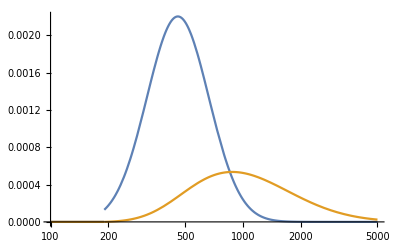

```mathematica
LogLinearPlot[{pdfx,pdfy},{x,100,5000},PlotRange->Full]
```

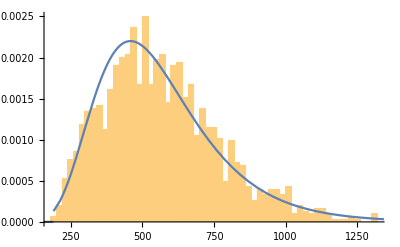

```mathematica
Show[Histogram[F1,50,"PDF"],Plot[pdfx,{x,100,1500}]]
```

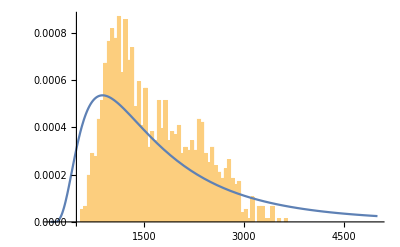

```mathematica
Show[Histogram[F2,50,"PDF"],Plot[pdfy,{x,100,5000}],PlotRange->Full]
```

```mathematica
pdfq=q[x,y,c,ρ,Ρ,σ,Σ]/.{c->190}/.sol//N//FullSimplify
```

Piecewise[{{1.23654×10^-63 ⅇ^(-3.65124 Log[x]^2-1.2848 Log[y/x]^2) x^42.2704 y^1.4846, x≥190.&&x≤y}, {0, True}}]

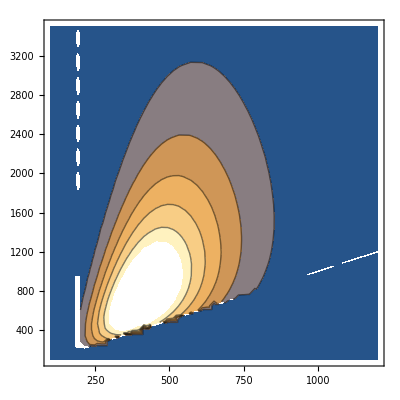

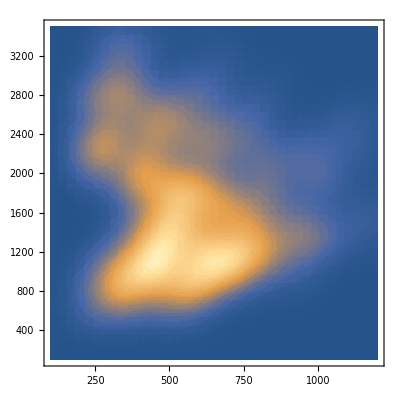

```mathematica
ContourPlot[pdfq,{x,100,1200},{y,100,3500}]
SmoothDensityHistogram[Transpose[{F1,F2}],Mesh->20,PlotRange->{{100,1200},{100,3500}}]
```

Compare joint pdf (contours) to data (smoothed density).

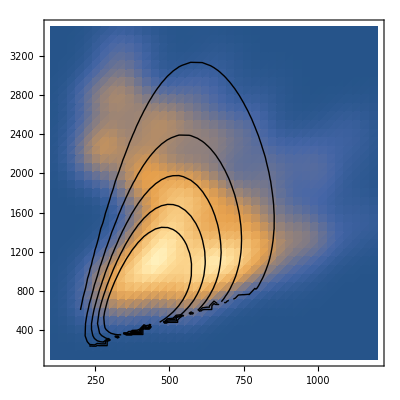

```mathematica
Show[SmoothDensityHistogram[Transpose[{F1,F2}],PlotRange->{{100,1200},{100,3500}}],ContourPlot[pdfq,{x,100,1200},{y,100,3500},ContourShading->None]]
```

Try to calculate moments of y again.

```mathematica
𝒟y=ProbabilityDistribution[pdfy,{x,-∞,∞}]
my=Mean[𝒟y]
vy=Variance[𝒟y]
```

ProbabilityDistribution[Piecewise[{{-7.53211×10^-23 x^12.7474 ⅇ^(-0.95038 Log[x]^2) (1. Erf[9.73804-1.64343 Log[x]]+Erf[1.91939-0.578291 Log[x]]), x>190}, {0, True}}],{x,-∞,∞}]

$Aborted

$Aborted

```mathematica
my=NExpectation[y,y\[Distributed]𝒟y]
vy=NExpectation[y^2,y\[Distributed]𝒟y]
sdev=Sqrt[vy-my^2]
```

1891.69

5.83875×10^6

1503.42

```mathematica
Mean[F2]//N
StandardDeviation[F2]//N
```

1624.38

637.013